## Динамические вычисления

```mathematica
myplot[a_,b_]:=Plot[{x^2+4x+a,Sin[b*x]},{x,-5,5},PlotRange->{{-5,5},{-5,25}},Epilog->{Red,PointSize@0.03,Point[{1,4}]},ImageSize->200]
```

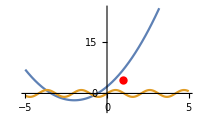

```mathematica
myplot[2,3]
```

```mathematica
Manipulate[myplot[a,b],{a,1,10},{b,1,10}](*manipulate для графики*)
```

```mathematica
D[ⅇ^(6x)*Cos[5x],{x,2}]
```

11 ⅇ^(6 x) Cos[5 x]-60 ⅇ^(6 x) Sin[5 x]

```mathematica
Manipulate[D[ⅇ^(6x)*Cos[5x],{x,a}],{a,1,10,1}]
```

```mathematica
Manipulate[ListPlot[{#,∑_(i=0)^# (-1)^i/(2i+1)}&/@Range[1,a]],{a,{1,5,10,30,50}}]
```

```mathematica
Manipulate[MatrixForm[{#,∑_(i=0)^# (-1)^i/(2i+1)}&/@Range[1,a]],{a,{1,5,10,20}}]
```

```mathematica
ClearAll[myFib]
```

```mathematica
??myFib
```

```mathematica
myFib[1]:=1
myFib[2]:=1
myFib[n_]:=myFib[n-1]+myFib[n-2]
```

```mathematica
Join[{{"N","Time","Fib"}},Flatten[{#,Timing[myFib[#]]}]&/@Range[1,25]]
```

{{N,Time,Fib},{1,0.,1},{2,0.,1},{3,0.,2},{4,0.,3},{5,0.,5},{6,0.,8},{7,0.,13},{8,0.,21},{9,0.,34},{10,0.,55},{11,0.,89},{12,0.,144},{13,0.,233},{14,0.,377},{15,0.,610},{16,0.,987},{17,0.,1597},{18,0.,2584},{19,0.015625,4181},{20,0.,6765},{21,0.015625,10946},{22,0.015625,17711},{23,0.015625,28657},{24,0.046875,46368},{25,0.09375,75025}}

```mathematica
Manipulate[Grid[Join[{{"N","Time","Fib"}},Flatten[{#,Timing[myFib[#]]}]&/@Range[1,a]],Frame->All,Background->{{LightBlue,LightGreen},None}],{a,{5,10,15,20,25,30,35}}]
```

```mathematica
circ[t_]:={Cos[t],Sin[t]}
astroid[t_]:={Cos[t]^3,Sin[t]^3}
```

```mathematica
giveAnimation[f_]:=Animate[Graphics[{Red,PointSize[0.03],Point[f[t]],Dashed,Line[f[#]&/@Range[0,t,0.01]]},PlotRange->{{-1,1},{-1,1}},ImageSize->150,Axes->True],{t,0,2π}]
```

```mathematica
bug[t_,a_:1]:={a*t-a*Sin[t],a-a*Cos[t]}
```

```mathematica
giveAnimation[bug]
```

```mathematica
bugGraphics[t_]:={Red,PointSize[0.03],Point[bug[t]],Dashed,Red,Line[bug[#]&/@Range[0,t,0.01]]}
```

```mathematica
wheelGraphics[t_]:={Thick,Black,Line[{{bug[t],{t,1}}}],Circle[{t,1},1]}
```

```mathematica
rainGraphics[t_]:={Blue,Disk[{t,9},{2,0.8}],Line[{#,#+RandomReal[{0,2}]*{-1,-2}}&/@Table[{i,9},{i,t-2,t+2,0.5}]]}
```

```mathematica
Manipulate[Animate[Graphics[{bugGraphics[t],wheelGraphics[t],If[a,rainGraphics[t]]},PlotRange->{{0,20},{0,10}},ImageSize->200,Axes->True],{t,0,6π}],{a,{True,False}}]
```

```mathematica
Animate[Graphics[{Red,PointSize[0.03],Point[bug[t]],Thick,Black,Line[{{bug[t],{t,1}}}],Circle[{t,1},1],Dashed,Red,Line[bug[#]&/@Range[0,t,0.01]],{Blue,Disk[{t,9},{2,0.8}],Line[{#,#+RandomReal[{0,2}]*{-1,-2}}&/@Table[{i,9},{i,t-2,t+2,0.5}]]}},PlotRange->{{0,20},{0,10}},ImageSize->200,Axes->True],{t,0,6π}]
```

```mathematica
{#,#+0.5*{1,2}}&/@Table[{i,9},{i,1-2,1+2,0.5}]
```

{{{-1.,9},{-0.5,10.}},{{-0.5,9},{0.,10.}},{{0.,9},{0.5,10.}},{{0.5,9},{1.,10.}},{{1.,9},{1.5,10.}},{{1.5,9},{2.,10.}},{{2.,9},{2.5,10.}},{{2.5,9},{3.,10.}},{{3.,9},{3.5,10.}}}

```mathematica
ListAnimate[Graphics[{bugGraphics[#],wheelGraphics[#],rainGraphics[#]},PlotRange->{{0,20},{0,10}},ImageSize->200,Axes->True]&/@Range[0,2,0.1]]
```